```mathematica
Quit[];
```

{1. (m+M) x''[t]+1. m R Cos[θ[t]] θ''[t]==1. m R Sin[θ[t]] θ'[t]^2,m R (-1. g Sin[θ[t]]+1. Cos[θ[t]] x''[t]+1. R θ''[t])==0}

{x''[t]==(m Sin[θ[t]] (1. g Cos[θ[t]]-1. R θ'[t]^2))/(-1. m-1. M+1. m Cos[θ[t]]^2),θ''[t]==(Sin[θ[t]] (-1. g m-1. g M+1. m R Cos[θ[t]] θ'[t]^2))/(R (-1. m-1. M+1. m Cos[θ[t]]^2))}

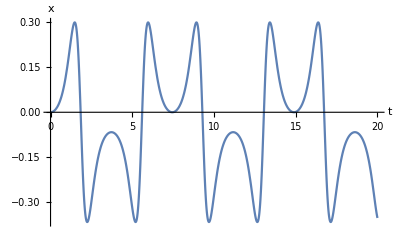

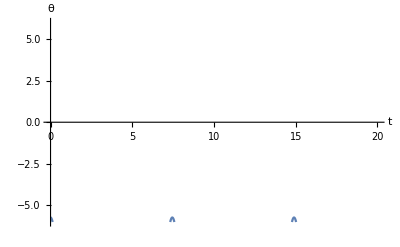

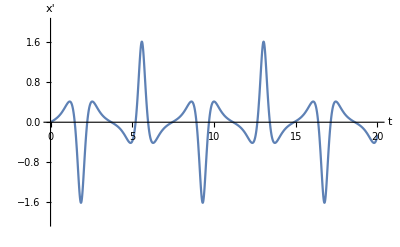

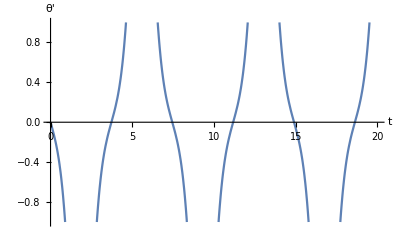

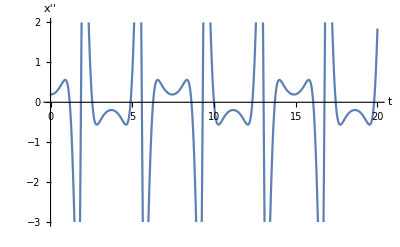

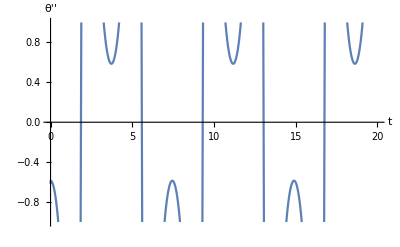

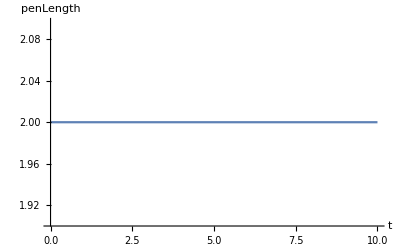

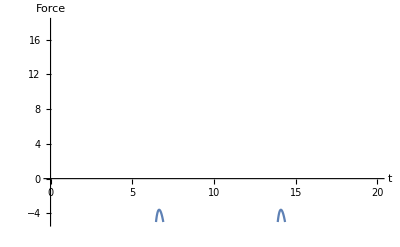

```mathematica
q={{x[t]},{θ[t]}};

(*FIRST AND SECOND TIME DERIVATIVES*)
dq=D[q,t];
ddq=D[dq,t];

(*LAGRANGIAN*)
PE=m*g*R*Cos[θ[t]];
KE= 0.5*(M+m)*x'[t]^2+0.5*m*(2*x'[t]*R*θ'[t]*Cos[θ[t]]+R^2*θ'[t]^2);
L=KE-PE;
(*F =   3.1623*(x[t]-0)+8.8286*x'[t]+179.4217*θ[t]+76.4998*θ'[t];*)
(*EULER LAGRANGE EQUATIONS*)
Eq=(Thread[D[D[L,dqᵀ],t]-D[L,qᵀ]=={0,0}])//FullSimplify

(*Always bring the equations in the form q''[t]=something*)
ELtemp=Solve[Eq[[1]]&&Eq[[2]],Flatten[ddq]];

(*Write Euler Lagrange equations in a list format because this is how NDSolve wants them!!*)
EL={x''[t]==ELtemp[[1,1,2]],θ''[t]==ELtemp[[1,2,2]]}//FullSimplify

(*PARAMETERS*)
(*Before using NDSolve you must assign values to all the parameters of the system!*)
m= 1;
M = 5;
R = 2;
g=9.8;
tend = 20;
(*INITIAL CONDITIONS*)
(*Set Initial conditions in a list format because this is how NDSolve wants them!!*)
InitCon={x'[0]==0, x[0]==0, θ[0]==-0.1, θ'[0]==0};

(*SOLVE THE DIFFERENTIAL EQUATIONS WITH NDSOLVE*)
(*Solve the equations of motion*)
sol=NDSolve[Join[EL,InitCon],{x,θ},{t,0,tend}] ;
solvel=NDSolve[Join[EL,InitCon],{x',θ'},{t,0,tend}] ;
solaccel=NDSolve[Join[EL,InitCon],{x'',θ''},{t,0,tend}] ;
(*Instead of {x,y} you could write q[[;;,1,0]]!!*)

(*ASSIGN THE NUMERICAL SOLUTIONS TO THE CONFIGURATION VARIABLES*)
(*assign the result to x[t]*)
xsol=x[t]/.sol[[1]];
θsol=θ[t]/.sol[[1]];
xsolvel=x'[t]/.solvel[[1]];
θsolvel=θ'[t]/.solvel[[1]];
xsolaccel=x''[t]/.solaccel[[1]];
θsolaccel=θ''[t]/.solaccel[[1]];

(*PLOTS*)
Plot[xsol,{t,0,tend}, AxesLabel->{t,x}]
Plot[θsol*180/Pi,{t,0,tend}, AxesLabel->{t,θ},PlotRange->{{0,tend},{-6,6}}]
Plot[xsolvel,{t,0,tend}, AxesLabel->{t,x'},PlotRange->{{0,tend},{-2,2}}]
Plot[θsolvel,{t,0,tend}, AxesLabel->{t,θ'},PlotRange->{{0,tend},{-1,1}}]
Plot[xsolaccel,{t,0,tend}, AxesLabel->{t,x''},PlotRange->{{0,tend},{-3,2}}]
Plot[θsolaccel,{t,0,tend}, AxesLabel->{t,θ''},PlotRange->{{0,tend},{-1,1}}]
Plot[Sqrt[((xsol+R*Sin[θsol])-xsol)^2 + (R*Cos[θsol])^2],{t,0,10},AxesLabel -> {t,penLength}]
Plot[3.1623*(xsol-0)+8.8286*xsolvel+179.4217*θsol+76.4998*θsolvel,{t,0,tend},AxesLabel ->{t,Force},PlotRange->{{0,tend},{-5,18}}]
(*ANIMATION*)
Xa[τ_]:=xsol/.t-> τ;
θa[τ_]:=θsol/.t-> τ;
finalSim = Table[Graphics[{Red,Rectangle[{Xa[τ]-.5,-.5}],Black,Thick,Line[{{Xa[τ],0},{Xa[τ]+R*Sin[θa[τ]],R*Cos[θa[τ]]}}], Blue,Disk[{Xa[τ]+R*Sin[θa[τ]],R*Cos[θa[τ]]},.2]},Axes->True,PlotRange->{{-3,3},{-3,3}}],{τ,0,tend,.05}];
Export["pure_dynamics.gif",finalSim,"AnimationRepetitions"-> ∞]
```